```mathematica
ClearAll["Global`*"]
```

Question 1

```mathematica
Ed[m_,ϵ_]:=(1.60217662*10^(-19))^4*m/(2*(4*Pi*ϵ*8.854*10^(-12)*1.055*10^(-34))^2)
```

```mathematica
m=0.015*9.10938356*10^(-31);ϵ=18;
```

```mathematica
Ed[m,ϵ]
```

1.00842×10^-22

```mathematica
ad[m_,ϵ_]:=4*Pi*ϵ*8.854*10^(-12)*(1.055*10^(-34))^2/(m*(1.60217662*10^(-19))^2)
```

```mathematica
R=ad[m,ϵ]
```

6.35515×10^-8

```mathematica
1/(4/3*Pi*R^3)
```

9.30109×10^20

Question 3

```mathematica
n=Sqrt[4*(1.38*10^(-23)*295/(2*Pi^2*(1.054*10^(-34))^2))^3*(0.32*0.47)^(3/2)*(9.109*10^(-31))^3*E^(-1.11/(8.617*10^(-5)*295))]
```

3.50126×10^14

```mathematica
n0=N[1/2*(10^21+Sqrt[(10^21)^2+4*n^2])]
```

1.×10^21

```mathematica
n^2/n0
```

1.22588×10^8

Question 4 - d

```mathematica
k[Ε_]:= Integrate[e/ℏ*Ε,{t,0,t1}];
vg[ϵ_ ]:=1/ℏ*Grad[ϵ,{kx,ky}];
x[vg_]:=Integrate[vg,{t1,0,t}];
```

```mathematica
ϵ=-Δ*(Cos[kx*a]+Cos[ky*a])
```

-Δ (Cos[a kx]+Cos[a ky])

```mathematica
Ε={E0,E0/3}
```

{E0,E0/3}

```mathematica
vg=vg[ϵ]
```

{(a Δ Sin[a kx])/ℏ,(a Δ Sin[a ky])/ℏ}

```mathematica
{kx,ky}=k[Ε]
```

{(e E0 t1)/ℏ,(e E0 t1)/(3 ℏ)}

```mathematica
vg
```

{(a Δ Sin[(a e E0 t1)/ℏ])/ℏ,(a Δ Sin[(a e E0 t1)/(3 ℏ)])/ℏ}

```mathematica
x=x[vg]
```

{(Δ-Δ Cos[(a e E0 t)/ℏ])/(e E0),(6 Δ Sin[(a e E0 t)/(6 ℏ)]^2)/(e E0)}

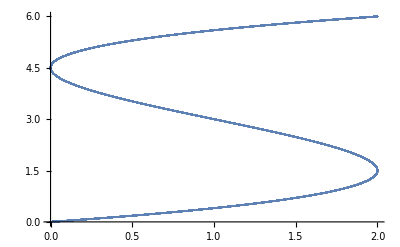

```mathematica
E0=a=Δ=1;e=1;(*1.60217662*10^(-19);*)
ℏ=1;(*1.054571800*10^(−34);*)ListPlot[Evaluate[Table[x,{t,0,25*Pi,0.001}]]]
```

```mathematica
Ε={E0,E0/Sqrt[3]}
```

{E0,E0/(√3)}

```mathematica
vg=vg[ϵ]
```

{(a Δ Sin[a kx])/ℏ,(a Δ Sin[a ky])/ℏ}

```mathematica
{kx,ky}=k[Ε]
```

{(e E0 t1)/ℏ,(e E0 t1)/(√3 ℏ)}

```mathematica
vg
```

{(a Δ Sin[(a e E0 t1)/ℏ])/ℏ,(a Δ Sin[(a e E0 t1)/(√3 ℏ)])/ℏ}

```mathematica
x=x[vg]
```

{(Δ-Δ Cos[(a e E0 t)/ℏ])/(e E0),-(√3 Δ (-1+Cos[(a e E0 t)/(√3 ℏ)]))/(e E0)}

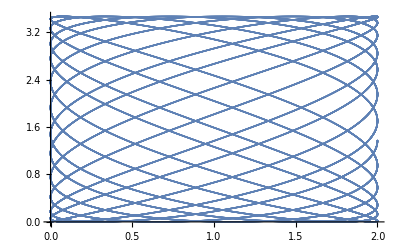

```mathematica
E0=a=Δ=1;e=1;(*1.60217662*10^(-19);*)
ℏ=1;(*1.054571800*10^(−34);*)ListPlot[Evaluate[Table[x,{t,0,25*Pi,0.001}]]]
```

```mathematica
Ε={E0,E0}
```

{E0,E0}

```mathematica
vg=vg[ϵ]
```

{(a Δ Sin[a kx])/ℏ,(a Δ Sin[a ky])/ℏ}

```mathematica
{kx,ky}=k[Ε]
```

{(e E0 t1)/ℏ,(e E0 t1)/ℏ}

```mathematica
vg
```

{(a Δ Sin[(a e E0 t1)/ℏ])/ℏ,(a Δ Sin[(a e E0 t1)/ℏ])/ℏ}

```mathematica
x=x[vg]
```

{(Δ-Δ Cos[(a e E0 t)/ℏ])/(e E0),(Δ-Δ Cos[(a e E0 t)/ℏ])/(e E0)}

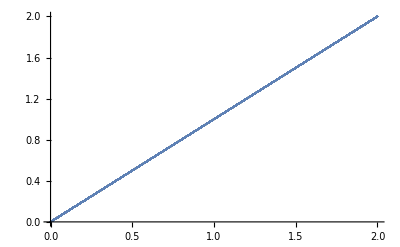

```mathematica
E0=a=Δ=1;e=1;(*1.60217662*10^(-19);*)
ℏ=1;(*1.054571800*10^(−34);*)ListPlot[Evaluate[Table[x,{t,0,25*Pi,0.001}]]]
```

```mathematica
x1={(Δ-Δ Cos[(a e E0 t)/ℏ+A]+B)/(e E0),(6 Δ Sin[(a e E0 t)/(6 ℏ)+c]^2+d)/(e E0)};E0=a=Δ=e=ℏ=1;A=1;B=1;
c=1;
d=1;
```

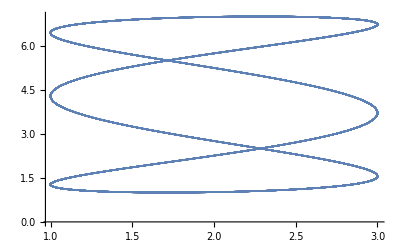

```mathematica
ListPlot[Evaluate[Table[x1,{t,0,25*Pi,0.001}]]]
```

```mathematica
x2={(Δ-Δ Cos[(a e E0 t)/ℏ])/(e E0),-(√3 Δ (-1+Cos[(a e E0 t)/(√3 ℏ)]))/(e E0)};
```

```mathematica
ListPlot[Evaluate[Table[x2,{t,0,25*Pi,0.001}]]]
```

-Graphics-

```mathematica
x3={(Δ-Δ Cos[(a e E0 t)/ℏ+1])/(e E0)+1,(Δ-Δ Cos[(a e E0 t)/ℏ+2])/(e E0)+0.1};
```

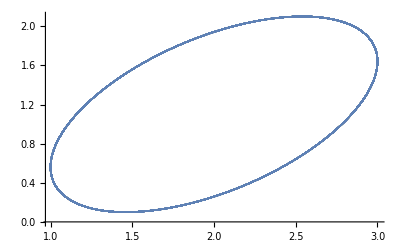

```mathematica
ListPlot[Evaluate[Table[x3,{t,0,25*Pi,0.001}]]]
```